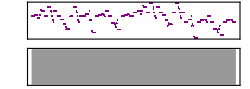

```mathematica
genSound[ music_]:=(
soundNoteList[list_]:= Apply[SoundNote, list];
generated = Map[soundNoteList, music];
sound = Sound[generated];
Return[sound];
)
ApplyAndJoin[fn_, count_]:=(
Flatten[Map[fn, Range[count]]]
)
ChooseTone[previous_,weights_,toneWeights_,toneImportance_,jumpBar_]:=(
allTones=Range[-Length[weights]+1 + previous,Length[weights]-1+previous];
allIntervalWeights=Join[Reverse[Drop[weights,1]],weights];
allToneWeights=Map[Function[t,Part[toneWeights,Mod[t, Length[toneWeights]] + 1]],allTones];
totalWeights = (allToneWeights * allIntervalWeights) ^ toneImportance;
Label[genNewTone];
tone = Part[RandomSample[totalWeights -> allTones, 1], 1];
If[RandomReal[]<DF[NormalDistribution[0, 0.1]][Abs[tone-previous]-jumpBar],
(Goto[genNewTone])];
Return[tone];
)
GetMelody[rythm_, weights_, toneWeights_] := (
melody = {0};
jumpBar = 6;
For[i=1, i<Length[rythm],i++, (
previous = melody[[i]];
next = ChooseTone[previous, weights, toneWeights, rythm[[i]] + 1, jumpBar];
jumpBar = Max[jumpBar, 100]-Abs[next-previous]+2.5;
AppendTo[melody, next];
)];
Return[melody];
)
CreateMusic[melody_, tones_, rythm_] := (
music = {};
For[i=1, i≤Length[melody],i++, (
toneOffset = melody[[i]];
tone = tones[[1+Mod[toneOffset,Length[tones]]]]+(Floor[toneOffset / Length[tones]] * 12);
sound = {tone, rythm[[i]] * 1.5, "Piano"};
AppendTo[music,sound];
)];
Return[music];
)
GetTact[divCoef_, recursionCoef_] := (
If[RandomReal[] > divCoef,(
Return[{1}]
),(
divLen[e_] := e / 2;
Return[ Map[divLen, Join[GetTact[divCoef / recursionCoef, recursionCoef], GetTact[divCoef/recursionCoef, recursionCoef]]]];
)]
)

GetRythm[divCoef_, recursionCoef_, size_] := 
ApplyAndJoin[Function[i, GetTact[divCoef, recursionCoef]], size]

rtm1 = GetRythm[2.3, 3,  1];
rtm2 = GetRythm[2.1, 2,  1];
tones = {0, 2,3, 5, 7, 8, 10} + 0;
weights = {1, 5, 5, 3, 3, 0.7,0.7, 1.2, 1};
toneWeights={1.7, 1.5, 1.6, 1, 1.6, 1.5, 1};
CmpM[rtm_]:=GetMelody[rtm, weights, toneWeights];
mainM = CmpM[rtm2];
melody1 = Join[CmpM[rtm1], ReplacePart[mainM, Length[rtm2]-> 4], CmpM[rtm1], ReplacePart[mainM, Length[rtm2]->0]];
mainM = CmpM[rtm1];
melody2 = Join[CmpM[rtm2], ReplacePart[mainM, Length[rtm1]-> 4], CmpM[rtm2], ReplacePart[mainM, Length[rtm1]->0]];

genSound[CreateMusic[Join[melody1, melody2, melody1+3, melody2-4],tones,ApplyAndJoin[Function[i, Join[rtm1, rtm2, rtm1, rtm2, rtm2, rtm1, rtm2, rtm1]], 2]]]
```

0.5

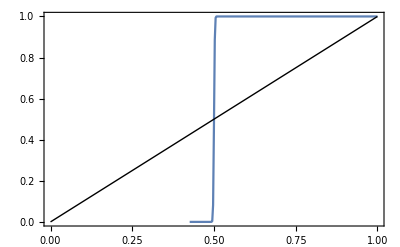

```mathematica
Round[CDF[NormalDistribution[0, 1]][0], 0.0001]
ProbabilityPlot[NormalDistribution[0, 0.005]]
```